# INTER-INTER-CODER RELIABILITY: LLM MULTISET ANALYSIS OF CONVID-19 MASK-WEARING SENTIMENT

```mathematica
Needs["ANOVA`"]
```

## IMPORTS

### TEST TWEETS

```mathematica
(*import tweet dataset*)
maskTweets = Import[FileNameJoin[{NotebookDirectory[],"data/mask_tweets.xlsx"}],{"Dataset",1},HeaderLines->1];
(*de-duplicate based on tweet ID*)
maskTweetsNoDuplicate = DeleteDuplicatesBy[maskTweets,"id"];
(*retweets removed*)
maskTweetsNoRetweet = maskTweets[;;,Append[#,<|"retweeted_status"->TrueQ[Head@#"retweeted_status"==Symbol]|>]&][Select[#"retweeted_status"==False&]];
(*retweets and duplicates removed*)
maskTweetsNoDuplicateNoRetweet = DeleteDuplicatesBy[maskTweetsNoRetweet,"id"];
(*IDs of mask tweets with multiples*)
maskIDMultiples = Select[ReverseSort@Dataset@Counts@Normal@maskTweets[;;,"id"],#>1&];

Tabular@maskTweetsNoDuplicateNoRetweet
```

### OVERALL DESCRIPTIVES

```mathematica
(*general tweet stats*)
Dataset[<|
"total tweets"-> Length@maskTweets,
"zip codes represented"->Length@DeleteDuplicates@maskTweets[;;,"zip"],
"retweets"-> Length@maskTweets[;;,Append[#,<|"retweeted_status"->TrueQ[Head@#"retweeted_status"==Symbol]|>]&][Select[#"retweeted_status"==True&]],
"duplicate tweets"->Length@maskTweets-Length@maskTweetsNoDuplicate,
"de-duplicated"->Length@maskTweetsNoDuplicateNoRetweet
|>]
```

### IMPORT & CLEAN STUDY DATA

```mathematica
llama370b=Import[#,"Dataset",HeaderLines->1]&/@FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data/output/llama3_70b"}]];
llama370bNoDuplicates = DeleteDuplicatesBy[#,"tweet_id"]&/@llama370b;
llama370bNoDuplicatesNoRetweets = Table[
t[Select[MemberQ[Normal@maskTweetsNoRetweet[;;,"id"],ToString@#"tweet_id"]&]][
;;,
Prepend[#,<|
"Column1"->ToExpression[#Column1],
"result"->ToExpression[#result],
"rationale"->#rationale,
"tweet_id"->#"tweet_id",
"eval_time"->ToExpression[#"eval_time"]
|>
]&],
{t,llama370bNoDuplicates}
];

phi314b=Import[#,"Dataset",HeaderLines->1]&/@FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data/output/phi3_14b"}]];
phi314bNoDuplicates = DeleteDuplicatesBy[#,"tweet_id"]&/@phi314b;
phi314bNoDuplicatesNoRetweets = Table[
t[Select[MemberQ[Normal@maskTweetsNoRetweet[;;,"id"],ToString@#"tweet_id"]&]][
;;,
Prepend[#,<|
"Column1"->ToExpression[#Column1],
"result"->ToExpression[#result],
"rationale"->#rationale,
"tweet_id"->#"tweet_id",
"eval_time"->ToExpression[#"eval_time"]
|>
]&],
{t,phi314bNoDuplicates}
];

gemma227b=Import[#,"Dataset",HeaderLines->1]&/@FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data/output/gemma2_27b"}]];
gemma227bNoDuplicates = DeleteDuplicatesBy[#,"tweet_id"]&/@gemma227b;
gemma227bNoDuplicatesNoRetweets = Table[
t[Select[MemberQ[Normal@maskTweetsNoRetweet[;;,"id"],ToString@#"tweet_id"]&]][
;;,
Prepend[#,<|
"Column1"->ToExpression[#Column1],
"result"->ToExpression[#result],
"rationale"->#rationale,
"tweet_id"->#"tweet_id",
"eval_time"->ToExpression[#"eval_time"]
|>
]&],
{t,gemma227bNoDuplicates}
];

mistral7b=Import[#,"Dataset",HeaderLines->1]&/@FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data/output/mistral_7b"}]];
mistral7bNoDuplicates = DeleteDuplicatesBy[#,"tweet_id"]&/@mistral7b;
mistral7bNoDuplicatesNoRetweets = Table[
t[Select[MemberQ[Normal@maskTweetsNoRetweet[;;,"id"],ToString@#"tweet_id"]&]][
;;,
Prepend[#,<|
"Column1"->ToExpression[#Column1],
"result"->ToExpression[#result],
"rationale"->#rationale,
"tweet_id"->#"tweet_id",
"eval_time"->ToExpression[#"eval_time"]
|>
]&],
{t,mistral7bNoDuplicates}
];

allDataNoDuplicatesNoRetweets = {llama370bNoDuplicatesNoRetweets,phi314bNoDuplicatesNoRetweets,gemma227bNoDuplicatesNoRetweets,mistral7bNoDuplicatesNoRetweets};
"models cleaned:"
Length@allDataNoDuplicatesNoRetweets
```

models cleaned:

4

## FUNCTIONS

## STATISTICAL

```mathematica
(*creates descriptive summary*)
DescriptiveAnalysis[data_,col_] := (
testData = Normal@#[;;,col]&/@data;
testDataOneWay = Flatten[#,1]&@Table[
Thread[{n,testData[[n]]}],
{n,Length@testData}
];
{
{testData,
testDataOneWay},
{Dataset@<|
"min"->Min/@testData,
"max"->Max/@testData,
"mean"->N@Mean/@testData,
"sd"->N@StandardDeviation/@testData
|>,
BoxWhiskerChart[testData]},
Dataset@<|
"min"->Min@Flatten@testData,
"max"->Max@Flatten@testData,
"mean"->N@Mean@Flatten@testData,
"sd"->N@StandardDeviation@Flatten@testData
|>
}
)

(*calculates entropies per each multiset response *)
ResponseEntropy[data_]:=Module[{d=data,sharedIndices,resultsCommon,resultsTransposed},
(*select only entries with all four (i.e., non parsing error) responses internal to datasets*)
sharedIndices = Intersection@@(Normal@#[;;,"Column1"]&/@d);
resultsCommon=#1[Select[MemberQ[sharedIndices,#"Column1"]&]]&/@d;
(*transpose so each entry is a single question's response*)
resultsTransposed = Transpose[Normal@#[;;,"result"]&/@resultsCommon];
resultsTransposed = Association@Thread[sharedIndices->resultsTransposed];
(*calculate entropy*)
resultsEntropy = N@Entropy[4,#]&/@resultsTransposed;
<|
"results"->resultsTransposed,
"result entropies"->resultsEntropy,
"dataset"->Dataset[<|
"all responses"->Length@First@resultsCommon,
"min entropy"->N@Min@resultsEntropy,
"max entropy"->N@Max@resultsEntropy,
"mean entropy"->N@Mean@resultsEntropy,
"sd entropy"->N@StandardDeviation@resultsEntropy
|>],
"freq."->KeySort@Dataset@Counts@resultsEntropy,
"prob."->KeySort@Dataset@N@(Counts@resultsEntropy/Length@First@resultsCommon),
"histogram"->Histogram[resultsEntropy,30,PlotRange->All]
|>
]

(*calculates JSON parsing syntax errors *)
JSONSyntaxErrors[data_]:=Module[{d=data},
allCounts = (KeySort[Counts[#1[;;,"result"]]]&)/@d;
hallucinatedColCounts = (Length@#[Select[!MemberQ[{-1,0,1,2,3},#result]&]]&)/@d;
hallucinatedCols = (Complement[Flatten@Normal@#[;;,"result"],{-1,0,1,2,3}]&)/@d;
allError = (KeySort[Counts[#[;;,"result"]/.x_/;StringQ[x]->-1]]&/@d);
<|
"all counts"->allCounts,
"Counts hallucinated cols"->hallucinatedColCounts,
"hallucinated cols"->hallucinatedCols,
"renames hallucinated cols to -1 and counts"->allError,
"descriptives"->Dataset[<|
"total err"->Total[(Length[#1[Select[#result==-1||!MemberQ[{-1,0,1,2,3},#result]&]]]&)/@d],
"mean err"->N[Mean[(Length[#1[Select[#result==-1||!MemberQ[{-1,0,1,2,3},#result]&]]]&)/@d]],
"sd err"->N[StandardDeviation[(Length[#1[Select[!MemberQ[{0,1,2,3},#result]&]]]&)/@d]]
|>],
"error"->(#1[Select[!MemberQ[{0,1,2,3},#result]&]]&)/@d,
"hallucinated"->(#1[Select[!MemberQ[{-1,0,1,2,3},#result]&]]&)/@d
|>
]

(*safe chi-squared with flare-out handling, test significance*)
SafeChiSquaredCategorical[data_(*lists of data*),categories_]:= Module[
{labels,counts,rowSums,colSums,total,expected,mask,chi2terms,chi2,df,p},
(*Your contingency table:rows=groups,columns=categories*)
labels = Union@@categories;
counts = Values@Counts[#,labels]&/@data;
rowSums=Total/@counts;
colSums=Total/@Transpose[counts];
total=Total[rowSums];
expected=Outer[#1 #2/total&,rowSums,colSums];
mask=Map[Positive,expected,{2}];
chi2terms=MapThread[If[#3,(#1-#2)^2/#2,0]&,{counts,expected,mask},2];
chi2=Total[Flatten[chi2terms]];;
(*chi2=Total[Flatten[(counts-expected)^2/expected]];*)
df=(Length[counts]-1)*(Length[First[counts]]-1);
p=1-CDF[ChiSquareDistribution[df],chi2];
<|"ChiSquaredStatistic"->N@chi2,"DegreesOfFreedom"->N@df,"PValue"->N@p|>
]

getDominantValue[list_]:=Module[
{counts,sorted,maxFreq,topValues},
counts=Tally[list];
sorted=SortBy[counts,-Last[#]&];
maxFreq=sorted[[1,2]];
topValues=Select[sorted,Last[#]==maxFreq&][[All,1]];
Which[Length[topValues]==1&&maxFreq>1,First[topValues],maxFreq>1,topValues,True,Nothing]
]

(*calculate Dunn's post-test for non parametric data (i.e., follows Kruskal-Wallis)*)
DunnPostTest[data_Association]:=Module[
{allData,n,dataGroupedIndex,sortedData,positions,rankMap,groupRanks,groupMeans,groupSizes,Ntotal,tieCounts,tieCorrection,keyPairs,dunnResults},
(*flattened data*)
allData = Association@Thread[Range@Length@Flatten@Values@data->Flatten@Values@data];
n=Length@allData;
(*indexed positions of data*)
dataGroupedIndex=Thread[Keys@data->TakeList[Range@Length@allData,Flatten[Dimensions/@Values@data]]];
(*sort all flattened data*)
sortedData=Sort[allData];
(*positions of flattened sorted data*)
positions=Thread[{Values@sortedData,Range@Length@sortedData}];
(*calculate tied ranks for mapping*)
(*rankMap=Flatten[Thread[First@@@#->N@Mean[Last@@@#]]&/@GatherBy[positions,First]];*)
rankMap=Table[
First@DeleteDuplicates[First/@p]->Mean[Last/@p],
{p,GatherBy[positions,First]}
];
(*group ranks*)
groupRanks=<|data/.rankMap|>;
groupMeans = Mean/@groupRanks;
groupSizes=Map[Length,data];
Ntotal=Total[Values[groupSizes]];
(*compute tie correction*)
tieCounts=Values@Counts[rankMap];
tieCorrection=Ntotal*(Ntotal+1)/(1-Total[(#^3-#)&/@tieCounts]/(Ntotal (Ntotal^2-1)));
(*calculate Dunn's*)
keyPairs=Subsets[Keys[data],{2}];
dunnResults=Table[
Module[
{i,j,Ri,Rj,ni,nj,z,se},
{i,j}=pair;
(*mean rank group i,j*)
Ri=groupMeans[i];
Rj=groupMeans[j];
(*size group i,j*)
ni=groupSizes[i];
nj=groupSizes[j];

se=Sqrt[(tieCorrection/12)* (1/ni+1/nj)];
z=(Ri-Rj)/se;
<|
"Group1"->i,
"Group2"->j,
"z"->N[z],
"p"->N[2 *(1-CDF[NormalDistribution[],Abs[z]])]
|>
],
{pair,keyPairs}
];
dunnResults
]
```

## INTERCODER ANALYSIS

```mathematica
KrippendorffsAlpha[coderData_List,distanceFunction_]:=Module[
{
data = coderData,
distFunc=distanceFunction,
units,pairableUnits,pairableUnitFrequencies,allPairs,allPairsAssoc,coincidencePairs,coincidencePairAssoc,coincidenceMatrix,do,de,alpha},
(*transpose lists of responses so they align by response*)
units =DeleteMissing/@(dataᵀ);
(*get all pairable units: non-missing units or units length > 1*)
pairableUnits = Select[units,Length@#>1&];
(*pairable unit frequencies: how often does each pairing occur?*)
pairableUnitFrequencies= Counts@Flatten[pairableUnits,1];
(*get all possible pairs:
 - flatten response units into a single set
- delete all duplicates
- get all possible pairings
- create association ID to identify pairs more easily*)
allPairs = Sort@Subsets[DeleteDuplicates@Flatten[units,1],{2}];
allPairsAssoc = AssociationThread[Range@Length@allPairs,allPairs];
(*get all coincidence (actual) pairs:
 - for all response units
	- get all possible pairings
	- flatten into list
	- create association ID to identify pairs more easily*)
coincidencePairs=DeleteDuplicates@Sort@Flatten[Table[
Sort/@Subsets[u,{2}],
{u,units}
],1];
coincidencePairAssoc=AssociationThread[Range@Length@coincidencePairs,coincidencePairs];
(*build coincidence matrix
- for each coinidence (actual) pair 
	- for all response units
		- if any paired subset of a response unit is a coincidence pair
		- for each case of coindicence pair that is in a pairing unit 
			- if same, increment buffer count by 2
			- else increment buffer count by 1/(length of unit -1)
	- total*)
coincidenceMatrix=Association@Table[
c->Total@Flatten[Table[
(*if any subset/pair in a unit is a coincidence pair*)
If[
MemberQ[Sort/@Subsets[u,{2}],coincidencePairAssoc[c]],
(*get all cases of subsets and check for pairwise agreement*)
(If[#[[1]]===#[[2]],2,1]&/@Cases[Sort/@Subsets[u,{2}],coincidencePairAssoc[c]])/(Length[u]-1),
0
],
{u,units}],1],
{c,Keys@coincidencePairAssoc}
];
(*observed distance:
 - for each coincidence pair
	- multiply disagreement of pair by frequency
*)
do=Sum[
coincidenceMatrix[c]*(distFunc@@coincidencePairAssoc[c]),
{c,Keys@coincidencePairAssoc}
];
(*expected distance:
 - for each possible pair
- multiply disagreement of pair by product of their frequencies
*)
de =Sum[
pairableUnitFrequencies[allPairsAssoc[c][[1]]]*pairableUnitFrequencies[allPairsAssoc[c][[2]]]*(distFunc@@allPairsAssoc[c]),
{c,Keys@allPairsAssoc}
]/((Length@Flatten[pairableUnits,1])-1);
(*alpha*)
alpha = N[1-(do/de)];
Dataset@<|"observed"->N@do,"expected"->N@de,"alpha"->N@alpha|>
]

NominalDistance[dataA_,dataB_]:=Module[
{a=dataA,b=dataB},
If[a===b,0,1]
]

MultisetDiceSørensenDistance[dataA_,dataB_]:=Module[
{a=dataA,b=dataB},
ResourceFunction["MultisetDiceDissimilarity"][a,b]
]

(*similarity between distributions*)
JensenShannonDistance[P_List,Q_List]:=Module[
{px,qx,X},
X = Union[P,Q];
px=AssociationThread[X,Lookup[Counts@P,X,0]]/Length@P;
qx=AssociationThread[X,Lookup[Counts@Q,X,0]]/Length@Q;
f[x_,y_] := If[x==0 ,0,x*Log[x/(.5*(x+y))]];
(.5*Sum[f[px[x],qx[x]],{x,X}] )+(.5*Sum[f[qx[x],px[x]],{x,X}])
]

WassersteinDistance1D[data1_,data2_,n_:1000]:=Module[
{p,q1,q2,raw,normed},
p=Range[0,1,1.0/n];
q1=Quantile[data1,p];
q2=Quantile[data2,p];
raw = Mean[Abs[q1-q2]];
normed = raw/(Max[Join[data1,data2]]-Min[Join[data1,data2]]);
<|{"raw"->raw,"normalized"->normed,"norm rescaled"->2*normed}|>
]
```

## MISC

```mathematica
(*retrieves final test dataset by overlap*)
MergeForSA[data_]:=Module[
{sharedIndices,sharedDatasets,truncatedTables},
(*select indices across datasets*)
sharedIndices = Intersection@@Flatten[(Normal@#1[;;,"Column1"]&/@#&/@Values@data),{2,1}];
sharedDatasets = #1[Select[MemberQ[sharedIndices,#"Column1"]&]]&/@#&/@data;
truncatedTables=Flatten@Table[
Table[
sharedDatasets[[k]][[d]][;;,Prepend[#,
<|
"index"->#"Column1",
"full_text"->#"full_text",
"result_"<>k<>"_"<>ToString@d->#"result",
"rationale_"<>k<>"_"<>ToString@d->#"rationale"
|>
]&][;;,;;4],
{d,Length@sharedDatasets[[k]]}
],
{k,Keys@sharedDatasets}
];
Fold[JoinAcross[#1,#2,{"index","full_text"}]&,truncatedTables]
]


n=30;
(*creates matrix plot with cell and axis labels*)
LabeledMatrixPlot[dataMatrix_List,matrixLabels_List,rotateLabel_:0Degree]:=Module[
{},
MatrixPlot[
Round[#,.01]&/@dataMatrix,
Epilog->Module[{n=Length[dataMatrix],rValues},rValues=Flatten[Table[Text[Style[Round[dataMatrix[[i,j]],.01],12,Black],{j-0.5,n-i+0.5}],{i,n},{j,n}]];
rValues],
FrameTicks->{{Thread[{Range@Length@dataMatrix,matrixLabels}],None},{None,Thread[{Range@Length@dataMatrix,Rotate[#,rotateLabel]&/@matrixLabels}]}},
FrameTicksStyle->14,
Frame->True,
AspectRatio->1,
ImageSize->500
]
]
```

## PROCESSING SPEED

## llama370b

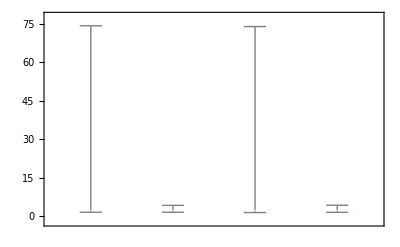

```mathematica
llama370bDesc = DescriptiveAnalysis[llama370bNoDuplicatesNoRetweets,"eval_time"];
llama370bDesc[[2;;]]
```

## gemma227b

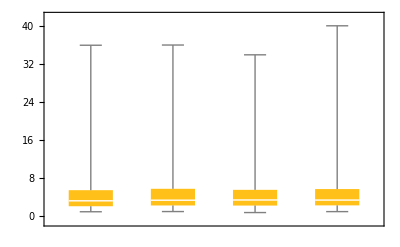

```mathematica
gemma227bDesc = DescriptiveAnalysis[gemma227bNoDuplicatesNoRetweets,"eval_time"];
gemma227bDesc[[2;;]]
```

## phi314b

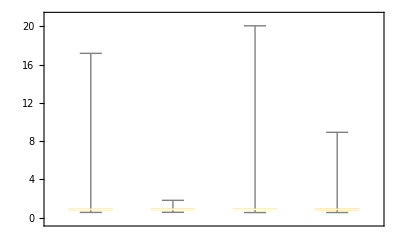

```mathematica
phi314bDesc = DescriptiveAnalysis[phi314bNoDuplicatesNoRetweets,"eval_time"];
phi314bDesc[[2;;]]
```

## mistral7b

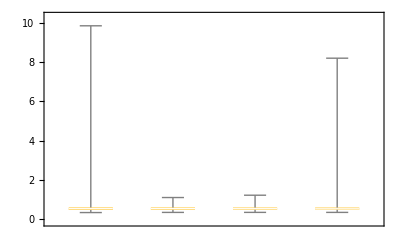

```mathematica
mistral7bDesc = DescriptiveAnalysis[mistral7bNoDuplicatesNoRetweets,"eval_time"];
mistral7bDesc[[2;;]]
```

## TWO-WAY

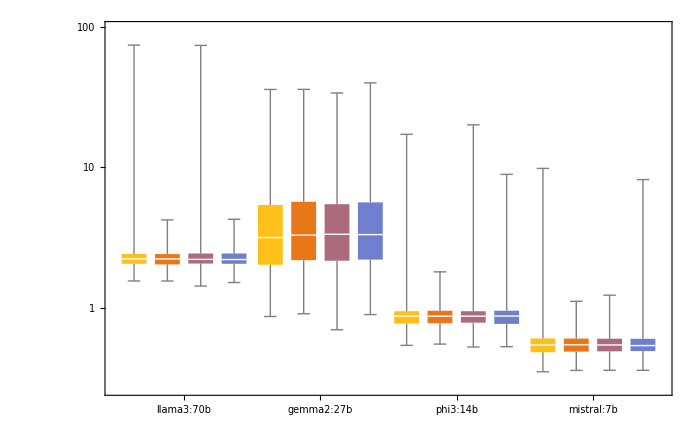

```mathematica
BoxWhiskerChart[{
Labeled[llama370bDesc[[1]][[1]],Style["llama3:70b",18]],
Labeled[gemma227bDesc[[1]][[1]],Style["gemma2:27b",18]],
Labeled[phi314bDesc[[1]][[1]],Style["phi3:14b",18]],
Labeled[mistral7bDesc[[1]][[1]],Style["mistral:7b",18]]
},
ScalingFunctions->"Log",
ImageSize->700
]
```

```mathematica
oneWayTable={
llama370bDesc[[1]][[1]],
phi314bDesc[[1]][[1]],
gemma227bDesc[[1]][[1]],
mistral7bDesc[[1]][[1]]
};

twoWayTable = Flatten[#,2]&@Table[
Table[
Append[{m,n},#]&/@oneWayTable[[m]][[n]],
{n,Length@oneWayTable[[m]]}],
{m,Length@oneWayTable}
];

ANOVA[twoWayTable,{x,y},{x,y},PostTests->{Bonferroni}]
```

General::munfl: Exp[-4185.03] is too small to represent as a normalized machine number; precision may be lost.

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
x | 3 | 38449.9 | 12816.6 | 3599.6 | 0.
y | 3 | 2.8854 | 0.961799 | 0.270125 | 0.846983
Error | 17177 | 61159.8 | 3.56057 |  | 
Total | 17183 | 99612.6 |  |  | ,CellMeans→All | 2.02389
x[1] | 2.2977
x[2] | 0.884547
x[3] | 4.35436
x[4] | 0.558963
y[1] | 2.00633
y[2] | 2.03183
y[3] | 2.01743
y[4] | 2.03997,PostTests→{x→Bonferroni | {{1,2},{1,3},{2,3},{1,4},{2,4},{3,4}},y→Bonferroni | {}}}

## SYNTAX ERRORS

## llama370b

```mathematica
llama370bErrors = JSONSyntaxErrors[llama370bNoDuplicatesNoRetweets];
llama370bErrors[[;;4]]
```

<|all counts→{,,,},Counts hallucinated cols→{0,0,0,0},hallucinated cols→{{},{},{},{}},renames hallucinated cols to -1 and counts→{,,,}|>

## gemma227b

```mathematica
gemma227bErrors = JSONSyntaxErrors[gemma227bNoDuplicatesNoRetweets];
gemma227bErrors[[;;4]]
```

<|all counts→{,,,},Counts hallucinated cols→{0,0,0,0},hallucinated cols→{{},{},{},{}},renames hallucinated cols to -1 and counts→{,,,}|>

## phi314b

```mathematica
phi314bErrors = JSONSyntaxErrors[phi314bNoDuplicatesNoRetweets];
phi314bErrors[[;;4]]
```

<|all counts→{,,,},Counts hallucinated cols→{0,0,0,0},hallucinated cols→{{},{},{},{}},renames hallucinated cols to -1 and counts→{,,,}|>

## mistral7b

```mathematica
mistral7bErrors = JSONSyntaxErrors[mistral7bNoDuplicatesNoRetweets];
mistral7bErrors[[;;4]]
```

<|all counts→{,,,},Counts hallucinated cols→{0,0,0,0},hallucinated cols→{{},{},{},{}},renames hallucinated cols to -1 and counts→{,,,}|>

## ERROR ANOVA

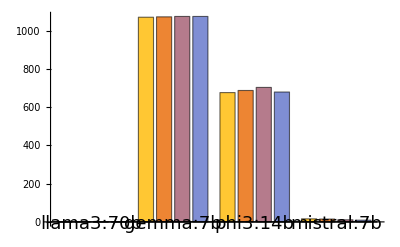

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
x | 3 | 3.34722×10^6 | 1.11574×10^6 | 27305.7 | 3.9487×10^-18
y | 3 | 114.75 | 38.25 | 0.936098 | 0.462599
Error | 9 | 367.75 | 40.8611 |  | 
Total | 15 | 3.3477×10^6 |  |  | ,CellMeans→All | 442.875
x[1] | 0.
x[2] | 1072.5
x[3] | 686.25
x[4] | 12.75
y[1] | 440.5
y[2] | 443.5
y[3] | 447.
y[4] | 440.5,PostTests→{x→Tukey | {{1,2},{1,3},{2,3},{2,4},{3,4}},y→Tukey | {}}}

```mathematica
syntaxErrorCounts =  <|
"llama3:70b"->{0,0,0,0},
"gemma:7b"->(#[Key[-1]]&/@gemma227bErrors["renames hallucinated cols to -1 and counts"]),
"phi3:14b"->(#[Key[-1]]&/@phi314bErrors["renames hallucinated cols to -1 and counts"]),
"mistral:7b"->(#[Key[-1]]&/@mistral7bErrors["renames hallucinated cols to -1 and counts"])
|>;

BarChart[
Labeled[#[[1]],Style[#[[2]],18]]&/@Thread[{Values@syntaxErrorCounts,Keys@syntaxErrorCounts}]
]

oneWayTableErrors=Values@syntaxErrorCounts;
twoWayTableErrors = Flatten[#,{1,2}]&@Table[
Table[
{m,n,oneWayTableErrors[[m]][[n]]},
{n,Length@oneWayTableErrors[[m]]}],
{m,Length@oneWayTableErrors}
];

ANOVA[twoWayTableErrors,{x,y},{x,y},PostTests->{Tukey}]
```

## ERRORS PER RESPONSE (ACROSS PASSES)

```mathematica
ErrorRepeatibility[data_,modelName_]:= Module[
{resultsTransposed,resultsTransposedError,errorCounts},
(*convert hallucinated result to -1 and transpose so each entry is a single question's response*)
(*resultsTransposed = Transpose[Normal@#[;;,"result"]/.x_/;StringQ[x]->-1&/@data];*)
resultsTransposed = Transpose[Normal@#[;;,"result"]&/@data];
(*select all questions containing a -1 response*)
resultsTransposedError = Select[resultsTransposed,MemberQ[#,-1]&];
(*count how many responses contain a -1 response*)
errorCounts = CountsBy[#1,#==-1&][True]&/@resultsTransposedError;
<|
"counts"->errorCounts,
"dataset"->Dataset[<|
"model"->modelName,
"err count"->Length@errorCounts,
"err count (%)"->(Length@errorCounts/(Dimensions@Normal@data)[[2]]),
"mean err"->If[errorCounts==={},"N/A",N@Mean@errorCounts],
"sd"->If[errorCounts==={},"N/A",N@StandardDeviation@errorCounts]
|>]
|>
]

errorRepeatabilities=<|
"llama370b"-> ErrorRepeatibility[llama370bNoDuplicatesNoRetweets,"llama3:70b"],
"gemma7b"->ErrorRepeatibility[gemma227bNoDuplicatesNoRetweets,"gemma:7b"],
"phi314b"-> ErrorRepeatibility[phi314bNoDuplicatesNoRetweets,"phi3:14b"],
"mistral7b"->ErrorRepeatibility[mistral7bNoDuplicatesNoRetweets,"mistral:7b"]
|>;

N#["dataset"]&/@errorRepeatabilities
```

<|llama370b→N ,gemma7b→N ,phi314b→N ,mistral7b→N |>

## SECOND CHANCE - RECOVER BY PATTERN MATCHING JSON

```mathematica
ParseJSONSecondChance[data_] := Module[
{d=data},
(*for each pass*)
Table[
(*for row in pass*)
dataOut = Dataset@Table[
(*extract subpattern from rationale if present*)
(*jsonPattern="\"result\":"~~___~~","~~"\"rationale\": \""~~Shortest[___]~~"\"";*)
jsonString = r["rationale"];
(*condense all whitespces into a single whitespace*)
jsonString = StringReplace[jsonString,("\n" | "\r"):>" "];
jsonString = StringReplace[jsonString,(WhitespaceCharacter~~WhitespaceCharacter..)->" "];
(*match json string pattern*)
zeroOrMoreWhitespace=(WhitespaceCharacter|"\n"|"\r")...;
jsonPattern=StringExpression["{",zeroOrMoreWhitespace,"\"result\"",zeroOrMoreWhitespace,":",zeroOrMoreWhitespace,___,zeroOrMoreWhitespace,",",zeroOrMoreWhitespace,"\"rationale\"",zeroOrMoreWhitespace,":",zeroOrMoreWhitespace,Shortest[___],zeroOrMoreWhitespace,"}"];
jsonList = StringCases[
jsonString,
jsonPattern,
1];
(*Print[jsonList];*)
(*if json is returned and No failure reported*)
If[
Length@jsonList > 0 && !FailureQ[Quiet@ImportString[First@jsonList,"JSON"]],
(*convert string to json*)
jsonAssoc=Association@ImportString[First@jsonList,"JSON"];
<|"result"->ToExpression@jsonAssoc["result"],"rationale"->jsonAssoc["rationale"],"Column1"->r["Column1"],"tweet_id"->r["tweet_id"],"full_text"->r["full_text"]|>,
Nothing
],
{r,Normal@d1}
];
dataOut[Select[MemberQ[{0,1,2,3},#["result"]]&]],
{d1,d}
]
]

Normal@#[;;,"rationale"]&/@phi314bErrors["error"];

phi314bErrorsSecondChance = ParseJSONSecondChance@phi314bErrors["error"];
gemma227bErrorsSecondChance = ParseJSONSecondChance@gemma227bErrors["error"];
mistral7bErrorsSecondChance = ParseJSONSecondChance@mistral7bErrors["error"];

Dataset@{
<|
"coder"->"llama370b",
"mean recovered"->"N/A",
"sd recovered"->"N/A"
|>,
<|
"coder"->"gemma227b",
"mean recovered"->(N@Mean[Length/@gemma227bErrorsSecondChance]),
"sd recovered"->(N@StandardDeviation[Length/@gemma227bErrorsSecondChance])
|>,
<|
"coder"->"phi314b",
"mean recovered"->(N@Mean[Length/@phi314bErrorsSecondChance]),
"sd recovered"->(N@StandardDeviation[Length/@phi314bErrorsSecondChance])
|>,
<|
"coder"->"mistral7b",
"mean recovered"->(N@Mean[Length/@mistral7bErrorsSecondChance]),
"sd recovered"->(N@StandardDeviation[Length/@mistral7bErrorsSecondChance])
|>}
```

## REINCORPORATE SECOND CHANCES

```mathematica
MergeSecondChance[data1_,data2_] := (
dataSecondChanceMerged = Table[
Join[
(*filter out errors only*)
data1[[n]][Select[MemberQ[{0,1,2,3},#result]&]],
(*reintroduce second chancers*)
data2[[n]]
][SortBy["Column1"]],
{n,Length@data1}
]
);

dataSecondChanceMergedNoErrors= <|
"llama370b"->(#1[Select[MemberQ[{0,1,2,3},#result]&]]&/@llama370bNoDuplicatesNoRetweets),
"gemma227b"->(MergeSecondChance[gemma227bNoDuplicatesNoRetweets,gemma227bErrorsSecondChance]),
"phi314b"->(MergeSecondChance[phi314bNoDuplicatesNoRetweets,phi314bErrorsSecondChance]),
"mistral7b"->(MergeSecondChance[mistral7bNoDuplicatesNoRetweets,mistral7bErrorsSecondChance])
(*"mistral7b"->(#1[Select[MemberQ[{0,1,2,3},#result]&]]&/@mistral7bNoDuplicatesNoRetweets)*)
|>;

Length/@#&/@dataSecondChanceMergedNoErrors
```

<|llama370b→{1074,1074,1074,1074},gemma227b→{577,550,546,572},phi314b→{1062,1066,1065,1062},mistral7b→{1065,1065,1068,1069}|>

## CODER COMPARISONS

### IMPORT HUMAN CODER DATA

```mathematica
files = FileNames["*.xlsx",FileNameJoin[{NotebookDirectory[],"data/output/human coders"}]]
humanCoderData= Association@Thread[Range@Length@#->#]&@(Import[#,{"Dataset",1},SkipLines->1,HeaderLines->1]&/@FileNames["*.xlsx",FileNameJoin[{NotebookDirectory[],"data/output/human coders"}]]);
humanCoderData=#[;;,Prepend[#,<|"index"->IntegerPart@#index,"full_text"->#"full_text","result"->ToExpression@StringTake[#result,1],"rationale"->#rationale|>]&]&/@humanCoderData
```

{/Users/natan/Documents/UC Shared/CIVIC TECH LAB/COVID LLM/WF PST presentation/data/output/human coders/data_merged_for_SA_human_coders_A.xlsx,/Users/natan/Documents/UC Shared/CIVIC TECH LAB/COVID LLM/WF PST presentation/data/output/human coders/data_merged_for_SA_human_coders_B.xlsx,/Users/natan/Documents/UC Shared/CIVIC TECH LAB/COVID LLM/WF PST presentation/data/output/human coders/data_merged_for_SA_human_coders_C.xlsx,/Users/natan/Documents/UC Shared/CIVIC TECH LAB/COVID LLM/WF PST presentation/data/output/human coders/data_merged_for_SA_human_coders_D.xlsx}

<|1→,2→,3→,4→|>

### PARSE FOR CODER COMPARISON

```mathematica
(*rename results column*)
Table[
humanCoderData[k][;;,Prepend[#,<|"result_"<>ToString@k->#"result"|>]&][;;,{"index","result_"<>ToString@k}],
{k,Keys@humanCoderData}
];
(*merge data*)
humanCoderResults = <|#index->Values@#[[2;;]]&/@Normal@Fold[JoinAcross[#1,#2,"index"]&,%]|>

(*get overlap list of indices for final analysis*)
dataMergedForSA = MergeForSA@dataSecondChanceMergedNoErrors;
finalIndices = Normal@dataMergedForSA[;;,"index"];
```

<|0→{0,3,3,0},1→{2,2,2,2},5→{3,2,3,2},9→{3,3,2,0},12→{2,2,2,2},17→{3,2,2,2},21→{1,1,1,1},24→{2,1,1,1},28→{0,0,2,0},40→{2,2,2,2},44→{3,0,3,0},48→{3,0,2,2},59→{3,0,2,0},63→{3,0,2,2},75→{1,1,1,1},78→{1,3,1,0},81→{1,1,1,1},115→{1,1,1,1},146→{0,0,2,0},169→{2,2,2,2},170→{1,1,1,1},176→{2,2,2,2},179→{0,0,3,2},181→{3,0,3,0},186→{1,0,1,1},192→{0,0,3,0},193→{1,2,2,0},196→{1,1,1,1},198→{1,2,2,2},205→{2,1,2,2},206→{2,2,2,2},207→{3,2,1,2},210→{3,0,3,0},213→{2,2,2,2},220→{3,0,2,0},246→{2,3,3,0},250→{1,2,1,0},257→{2,0,2,2},258→{3,3,3,2},280→{2,3,2,2},284→{3,1,1,0},285→{3,2,3,0},301→{0,0,0,0},307→{2,2,2,0},327→{2,0,2,0},328→{2,0,2,0},329→{2,2,2,0},339→{2,2,2,2},349→{0,0,0,0},355→{0,0,3,0},356→{2,1,3,2},370→{3,0,2,0},385→{3,3,3,0},387→{1,0,2,2},388→{2,1,1,0},393→{2,0,2,2},395→{2,2,2,2},396→{2,3,3,0},402→{2,3,2,2},414→{1,3,1,1},424→{3,0,3,0},425→{2,2,2,2},427→{2,2,2,0},436→{3,3,3,2},439→{1,1,1,0},441→{3,3,3,0},449→{3,0,2,0},454→{1,1,1,0},455→{3,3,3,0},460→{1,2,1,0},464→{2,3,2,0},470→{2,2,2,2},473→{1,1,1,0},474→{1,0,1,2},477→{2,2,2,2},478→{3,0,2,2},481→{2,0,2,2},484→{3,0,2,2},488→{0,0,2,0},490→{2,0,2,2},491→{2,1,1,0},513→{2,0,2,2},540→{1,1,3,0},544→{2,2,2,2},557→{1,1,1,0},570→{2,2,1,2},576→{2,3,2,2},586→{3,3,2,2},587→{2,0,3,0},596→{2,0,2,2},604→{2,2,2,0},612→{2,0,2,2},619→{2,0,1,0},620→{2,2,2,2},623→{0,0,2,0},627→{3,1,1,1},643→{2,2,2,2},645→{2,0,2,2},646→{2,2,2,2},654→{2,0,2,2},655→{2,0,2,0},657→{2,2,2,2},664→{3,1,1,0},669→{2,0,2,2},673→{3,1,2,2},675→{3,0,3,0},680→{1,1,1,1},681→{1,1,2,1},685→{2,2,2,2},687→{2,2,2,2},688→{1,1,1,1},697→{2,2,2,2},708→{3,2,2,0},713→{0,0,0,0},720→{2,2,2,2},731→{3,0,3,2},741→{2,2,2,2},743→{2,1,2,0},747→{2,2,2,2},751→{3,0,3,0},754→{0,0,3,0},757→{3,0,3,0},761→{3,0,3,2},772→{2,2,2,2},774→{2,2,2,2},775→{2,2,2,2},784→{3,1,3,0},785→{2,0,3,2},793→{2,2,2,2},794→{2,0,2,2},802→{2,2,2,2},803→{2,0,2,2},815→{3,0,2,2},848→{2,2,2,2},892→{1,0,1,0},894→{3,2,2,2},898→{1,0,1,1},906→{2,0,2,2},1126→{2,0,2,2},1129→{2,2,2,0},1138→{2,2,2,2},1339→{2,1,2,2},1340→{2,1,2,0},1346→{2,3,2,1},1425→{2,3,2,2},1457→{2,0,2,2},1461→{2,0,2,2},1481→{3,1,2,2},1498→{3,0,2,2},1499→{3,0,2,2},1517→{0,0,3,0},1519→{2,1,1,0},1522→{2,2,2,2},1525→{2,0,2,2},1548→{3,1,1,0},1638→{2,2,2,2},1639→{2,2,2,2},1651→{2,2,2,2},1657→{2,0,2,2},1665→{3,0,3,0},1666→{1,1,1,1},1670→{3,0,3,0},1693→{2,2,2,2},1707→{2,2,2,2},1708→{2,2,2,2},1722→{3,0,3,0},1733→{2,2,2,2},1746→{3,0,3,0},1747→{2,2,2,2},1748→{2,2,2,2},1765→{2,2,2,2},1766→{3,2,2,0},1767→{3,2,3,0},1769→{1,2,2,0},1775→{3,0,3,0},1828→{3,0,3,0},1830→{3,0,2,2},1838→{1,1,1,1},1839→{3,0,3,0},1885→{2,2,2,2},1894→{2,2,2,2},1896→{3,0,3,0},1900→{1,1,1,1},1901→{2,2,2,2},1935→{1,1,1,1},1940→{3,1,1,1},1942→{2,2,2,0},1951→{3,0,3,2},1953→{2,0,2,0},1958→{3,3,3,0},1986→{2,2,2,2},1987→{2,0,2,0},2024→{2,2,2,2},2028→{2,2,2,2},2029→{3,0,3,0},2046→{2,0,2,2},2051→{1,1,3,0},2052→{2,2,3,0},2053→{2,0,1,0},2061→{3,0,2,2},2062→{2,2,2,2},2064→{2,2,2,2},2079→{2,0,2,2},2112→{2,2,2,2},2172→{2,0,3,2},2174→{2,2,2,2},2205→{3,0,2,0},2213→{1,3,2,0},2229→{2,2,2,0},2231→{2,2,2,2},2243→{2,0,2,2},2262→{2,2,2,2},2265→{1,1,1,1},2272→{1,1,1,1},2281→{1,3,2,2},2292→{2,0,2,2},2312→{1,0,1,0},2337→{1,0,1,0},2340→{2,2,2,0},2344→{1,0,1,1},2354→{3,0,2,2},2452→{2,2,2,2},2509→{1,1,1,0},2511→{3,0,3,2},2513→{2,0,2,2},2525→{1,0,2,0},2566→{2,0,2,0}|>

### FINAL DATA

```mathematica
(*compile final results for all coders*)
finalResults=Prepend[Association@Table[
k->(responseEntropies[k]["results"][#]&/@finalIndices),
{k,Keys@responseEntropies}
],"human"->Values@humanCoderResults];
```

### RESPONSE COUNTS

#### DOMINANT OCURRENCES

( |  |  |  | 
human | llama370b | gemma227b | phi314b | mistral7b)

{{0, 0, 0, 0}→1,{0, 0, 0, 1}→2,{0, 0, 0, 2}→3,{0, 0, 0, 3}→4,{0, 0, 1, 1}→5,{0, 0, 1, 2}→6,{0, 0, 1, 3}→7,{0, 0, 2, 2}→8,{0, 0, 2, 3}→9,{0, 0, 3, 3}→10,{0, 1, 1, 1}→11,{0, 1, 1, 2}→12,{0, 1, 1, 3}→13,{0, 1, 2, 2}→14,{0, 1, 2, 3}→15,{0, 1, 3, 3}→16,{0, 2, 2, 2}→17,{0, 2, 2, 3}→18,{0, 2, 3, 3}→19,{0, 3, 3, 3}→20,{1, 1, 1, 1}→21,{1, 1, 1, 2}→22,{1, 1, 1, 3}→23,{1, 1, 2, 2}→24,{1, 1, 2, 3}→25,{1, 1, 3, 3}→26,{1, 2, 2, 2}→27,{1, 2, 2, 3}→28,{1, 2, 3, 3}→29,{1, 3, 3, 3}→30,{2, 2, 2, 2}→31,{2, 2, 2, 3}→32,{2, 2, 3, 3}→33,{2, 3, 3, 3}→34,{3, 3, 3, 3}→35}

CHI-SQUARED--------------------------------------------------------------------------------

<|ChiSquaredStatistic→743.434,DegreesOfFreedom→128.,PValue→0.|>

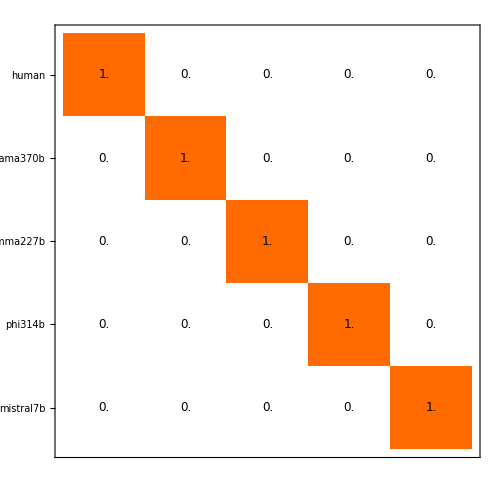

```mathematica
dominantOccurrenceCounts=(Dataset@ReverseSort@Counts[#])&/@(Sort/@#&/@Values@finalResults);
MatrixForm[{#&/@dominantOccurrenceCounts,Keys@finalResults},TableDirections->Column]

TextString/@DeleteDuplicates[Sort/@Tuples[Range[0,3],{4}]];
categoriesDominantOccurrences= Thread[%->Range@Length@%]

(*make categorical for comparison*)
dominantOccurrencesCategorical = Association@Table[
k->(TextString@(Sort@#)&/@finalResults[k])/.categoriesDominantOccurrences,
{k,Keys@finalResults}
];

"CHI-SQUARED--------------------------------------------------------------------------------"
SafeChiSquaredCategorical[Values@dominantOccurrencesCategorical,Values@dominantOccurrencesCategorical]

chiMatrix = Table[
SafeChiSquaredCategorical[{dominantOccurrencesCategorical[i],dominantOccurrencesCategorical[j]},Values@dominantOccurrencesCategorical]["PValue"],
{i,Keys@dominantOccurrencesCategorical},{j,Keys@dominantOccurrencesCategorical}
];

LabeledMatrixPlot[chiMatrix,Keys@finalResults,45Degree]
```

#### DOMINANT VALUES

( |  |  |  | 
human | llama370b | gemma227b | phi314b | mistral7b)

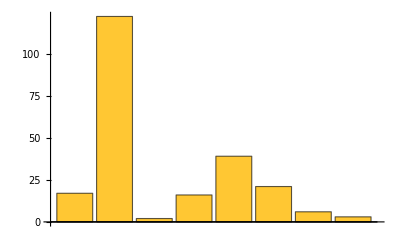
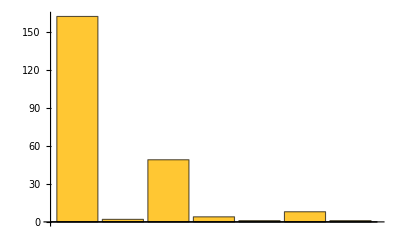
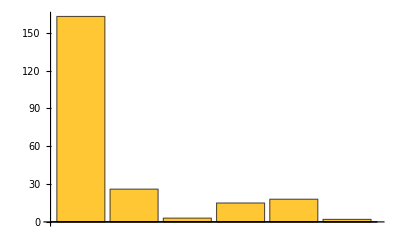
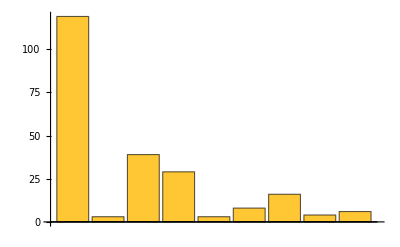
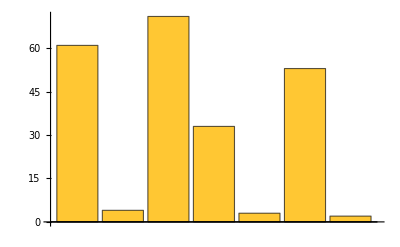
<|human→-Graphics-,llama370b→-Graphics-,gemma227b→-Graphics-,phi314b→-Graphics-,mistral7b→-Graphics-|>

CHI-SQUARED--------------------------------------------------------------------------------

all→0.

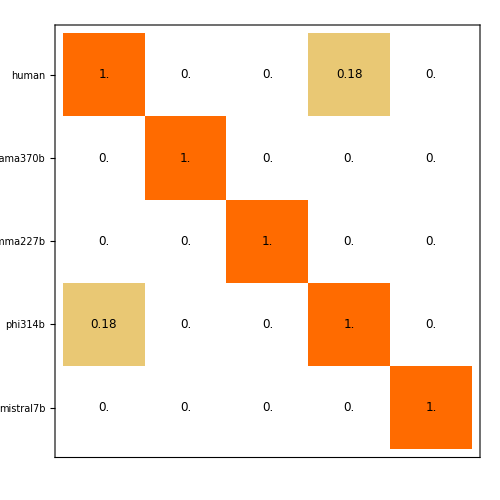

```mathematica
dominantValues = Association@Table[
k->getDominantValue/@finalResults[k],
{k,Keys@finalResults}
];
dominantValuesCounts = (Dataset@ReverseSort@Counts[#])&/@Values@dominantValues;
MatrixForm[{#[;;5]&/@dominantValuesCounts,Keys@finalResults},TableDirections->Column]

(*make categorical for comparison*)
categoriesDominantValue =Thread[TextString/@Sort@DeleteDuplicates@Flatten[Values@dominantValues,1]->Range@Length@DeleteDuplicates@Flatten[Values@dominantValues,1]];

dominantValuesCategorical = Association@Table[
k->(First@StringReplace[TextString[#],categoriesDominantValue]&/@dominantValues[k]),
{k,Keys@dominantValues}
];

BarChart[Counts[ToString/@#]]&/@dominantValues

"CHI-SQUARED--------------------------------------------------------------------------------"
"all"->SafeChiSquaredCategorical[Values@dominantValuesCategorical,Values@dominantValuesCategorical]["PValue"]
chiMatrixDominantValue = Table[
SafeChiSquaredCategorical[{dominantValuesCategorical[i],dominantValuesCategorical[j]},Values@dominantValuesCategorical]["PValue"],
{i,Keys@dominantValuesCategorical},{j,Keys@dominantValuesCategorical}
];

LabeledMatrixPlot[chiMatrixDominantValue,Keys@finalResults,45Degree]
```

### ENTROPIES

#### CALCULATE ENTROPIES

compare overall/mean entropies

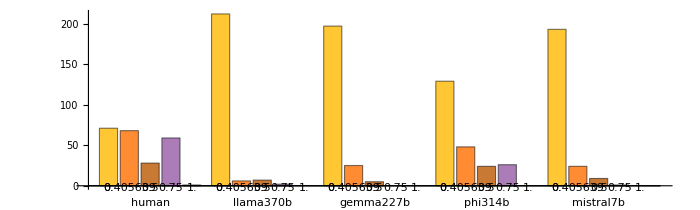

```mathematica
"compare overall/mean entropies"
modelEntropiesCompare=<|
"human"->Values[(N@Entropy[4,#]&/@humanCoderResults)],
"llama370b"->(N@Entropy[4,#]&/@Normal@Values@dataMergedForSA[;;,{"result_llama370b_1","result_llama370b_2","result_llama370b_3","result_llama370b_4"}]),
"gemma227b" -> (N@Entropy[4,#]&/@Normal@Values@dataMergedForSA[;;,{"result_gemma227b_1","result_gemma227b_2","result_gemma227b_3","result_gemma227b_4"}]),
"phi314b" -> (N@Entropy[4,#]&/@Normal@Values@dataMergedForSA[;;,{"result_phi314b_1","result_phi314b_2","result_phi314b_3","result_phi314b_4"}]),
"mistral7b" -> (N@Entropy[4,#]&/@Normal@Values@dataMergedForSA[;;,{"result_mistral7b_1","result_mistral7b_2","result_mistral7b_3","result_mistral7b_4"}])
|>;

Table[
<|
"coder"->m,
"# agree"->(KeySort@Counts[modelEntropiesCompare[m]])[0.],
"% agree"->N@(KeySort@Counts[modelEntropiesCompare[m]])[0.]/Length@modelEntropiesCompare[m],
"min"->Min@modelEntropiesCompare[m],
"max"->Max@modelEntropiesCompare[m],
"mean"->Mean@modelEntropiesCompare[m],
"sd"->StandardDeviation@modelEntropiesCompare[m],
"median"->Median@modelEntropiesCompare[m],
"qd"->QuartileDeviation@modelEntropiesCompare[m]
|>
,
{m,Keys@modelEntropiesCompare}
];

modelEntropiesCompareDescriptives = Dataset@(%ᵀ)

BarChart[
(KeySort/@Counts/@modelEntropiesCompare),
ChartLabels->Automatic,
LabelStyle->14,
PlotRange->All,
AspectRatio->.3,
ImageSize->700
]
```

#### COMPARE ENTROPIES

```mathematica
(*compareEntropies=Prepend[KeyTake[#,finalIndices]&/@responseEntropies[[;;,"result entropies"]],"human"->humanCoderEntropies]*)

LocationEquivalenceTest[
Values@modelEntropiesCompare,
"TestDataTable"
]

Dataset@DunnPostTest[modelEntropiesCompare]
```

| Statistic | P-Value
Kruskal-Wallis | 317.185 | 4.95357×10^-79

#### CORRELATE ENTROPIES ACROSS REPONSES

SPEARMAN'S R--------------------------------------------------

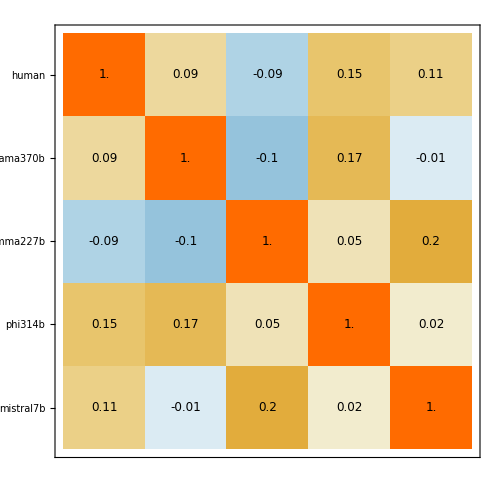

```mathematica
"SPEARMAN'S R--------------------------------------------------"
correlationMatrixEntropiesSpearmans=Table[
SpearmanRho[modelEntropiesCompare[i],modelEntropiesCompare[j]],
{i,Keys@modelEntropiesCompare},{j,Keys@modelEntropiesCompare}
];

LabeledMatrixPlot[correlationMatrixEntropiesSpearmans,Keys@modelEntropiesCompare,45Degree]
```

#### WASSERSTEIN’S 1D (EARTH-MOVING DISTANCE)

{{0.,0.69928,0.653489,0.316387,0.633066},{0.69928,0.,0.0815886,0.510523,0.0936126},{0.653489,0.0815886,0.,0.449469,0.0272309},{0.316387,0.510523,0.449469,0.,0.422238},{0.633066,0.0936126,0.0272309,0.422238,0.}}

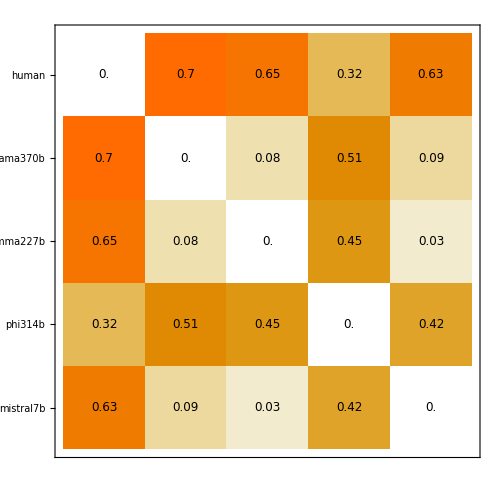

```mathematica
distanceMatrixEntropiesWasserstein=Table[
WassersteinDistance1D[modelEntropiesCompare[i],modelEntropiesCompare[j]]["norm rescaled"],
{i,Keys@modelEntropiesCompare},{j,Keys@modelEntropiesCompare}
]

LabeledMatrixPlot[distanceMatrixEntropiesWasserstein,Keys@modelEntropiesCompare,45Degree]
```

#### UNCERTAIN RESPONSE ENTROPIES

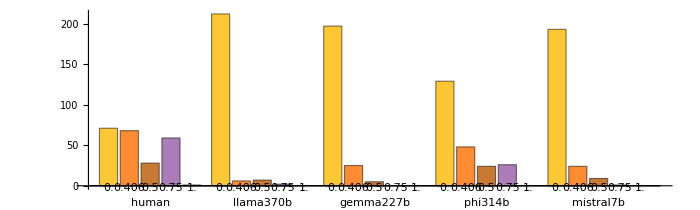

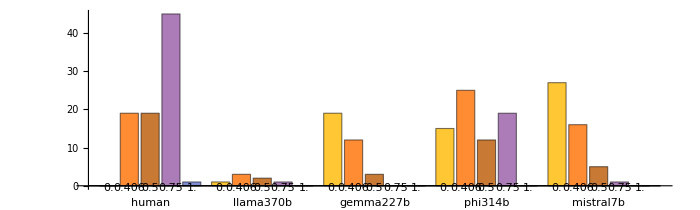

```mathematica
finalResultsUncertain = (Select[#,MemberQ[3]]&/@finalResults);
finalResultsUncertainEnropies = N@Entropy[4,#]&/@#&/@finalResultsUncertain;

BarChart[
KeyMap[Round[#,.001]&,#]&/@(KeySort/@Counts/@modelEntropiesCompare),
ChartLabels->Automatic,
LabelStyle->10,
AspectRatio->.3,
ImageSize->700,
PlotRange->All
]

KeyMap[Round[#,.001]&,#]&/@Association@Table[
k->AssociationThread[Sort@DeleteDuplicates@Flatten@Values@finalResultsUncertainEnropies,Lookup[Counts@finalResultsUncertainEnropies[k],#,0]&/@Sort@DeleteDuplicates@Flatten@Values@finalResultsUncertainEnropies],
{k,Keys@finalResultsUncertainEnropies}
];

BarChart[
%,
ChartLabels->Automatic,
PlotRange->50,
PlotLabel->"",
LabelStyle->10,
AspectRatio->.3,
ImageSize->700
]

HypothesisTestPermute[child_List,parent_List,func_Function] := Module[
{complement,to,tiList,p},
complement=DeleteCases[parent,Alternatives@@child,1,Length[child]];
to = func[{child,complement}];
tiList=Table[func[
{child,RandomSample[#,Length@child]&@parent}
],100000];
p=N[Count[tiList,x_/;Abs[x]>=Abs[to]]+1]/(Length[tiList]+1);
<|"statistic"->to,"p"->p|>
]

Dataset@WassersteinDistance1D[modelEntropiesCompare["gemma227b"],modelEntropiesCompare["llama370b"]]

Dataset@Table[
<|
"coder"->k,
"# of resp. (pass)"->Length@finalResultsUncertainEnropies[k],
"% of resp. (pass)"->N[Length@finalResultsUncertainEnropies[k]/Length@finalResults[k]],
"min entropy"->Min[finalResultsUncertainEnropies[k]],
"max entropy"->Max[finalResultsUncertainEnropies[k]],
"mean entropy"->Mean[finalResultsUncertainEnropies[k]],
"sd"->StandardDeviation[finalResultsUncertainEnropies[k]],
"median entropy"->Median[finalResultsUncertainEnropies[k]],
"qd"->QuartileDeviation[finalResultsUncertainEnropies[k]],
"Mann-Whitney permuted"->HypothesisTestPermute[finalResultsUncertainEnropies[k],modelEntropiesCompare[k],MannWhitneyTest]
|>,
{k,Keys@finalResultsUncertain}
]
```

{ | Statistic | P-Value
Kruskal-Wallis | 99.7467 | 2.03128×10^-26}

Dunn post-test

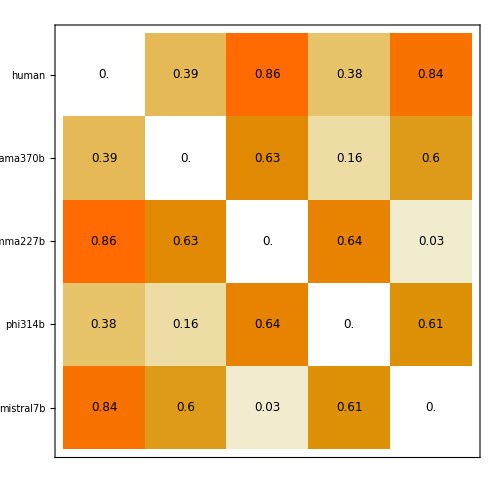

```mathematica
LocationEquivalenceTest[Values@finalResultsUncertainEnropies,{"TestDataTable"}]
"Dunn post-test"
Dataset@DunnPostTest[finalResultsUncertainEnropies]

distanceMatrixUncertainEntropiesWasserstein=Table[
WassersteinDistance1D[finalResultsUncertainEnropies[i],finalResultsUncertainEnropies[j]]["norm rescaled"],
{i,Keys@modelEntropiesCompare},{j,Keys@modelEntropiesCompare}
];

LabeledMatrixPlot[distanceMatrixUncertainEntropiesWasserstein,Keys@modelEntropiesCompare,45Degree]
```

## INTERCODER ANALYSIS

### KRIPPENDORF’S ALPHA (NOMINAL/INTRA CODER)

```mathematica
krippendorffsInternal = Table[
Prepend[KrippendorffsAlpha[finalResults[r]ᵀ,NominalDistance],<|"coder"->r|>],
{r,Keys@finalResults}
]
```

{,,,,}

### MULTISET COMPARISONS

#### SØRENSEN-DICE

obtains the length of the response-to-response multiset overlap of each; i.e. ithe length of any of the subset that matches. The higher the value, the more similar.

Dice-Sørensen distances per response

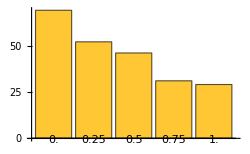
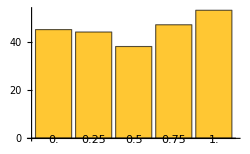
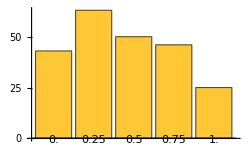
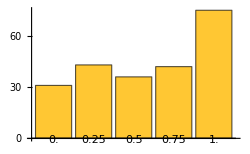
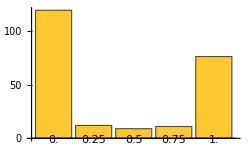
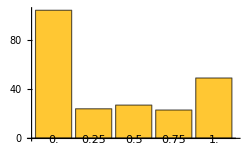
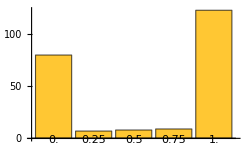
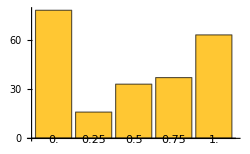
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0

```mathematica
"obtains the length of the response-to-response multiset overlap of each; i.e. ithe length of any of the subset that matches. The higher the value, the more similar."

(*obtain Dice-Sorenson coefficients*)
"Dice-Sørensen distances per response"
finalMultisetDice= Association@Table[
s->MapThread[N@(MultisetDiceSørensenDistance[#1,#2])&,{finalResults[s[[1]]],finalResults[s[[2]]]}],
{s,Subsets[Keys@finalResults,{2}]}
];

Dataset@Table[
<|
"comp."->k[[1]]<>"/"<>k[[2]],
"min"->ToString@ResourceFunction["DecimalRound"][N@Min@#,3]&@finalMultisetDice[k],
"max"->ToString@ResourceFunction["DecimalRound"][N@Max@#,3]&@finalMultisetDice[k],
"mean"->ToString@ResourceFunction["DecimalRound"][N@Mean@#,2]<>" (sd="<>ToString@ResourceFunction["DecimalRound"][N@StandardDeviation@#,2]<>")"&@finalMultisetDice[k],
"median"->ToString@ResourceFunction["DecimalRound"][N@Median@#,2]<>" (qd="<>ToString@ResourceFunction["DecimalRound"][N@QuartileDeviation@#,2]<>")"&@finalMultisetDice[k]
|>,
{k,Keys@finalMultisetDice}
]

DisplayForm@GridBox@ArrayReshape[#,{4,3}]&@Table[
Labeled[BarChart[#,PlotRange->150,ChartLabels->Keys@#,ImageSize->250],Style[k,14],Bottom]&@KeySort@Counts@finalMultisetDice[k],
{k,Keys@finalMultisetDice}
]
```

| Statistic | P-Value
Kruskal-Wallis | 137.966 | 3.99957×10^-26

dunn post-test--------------------------------------------------------------------------------

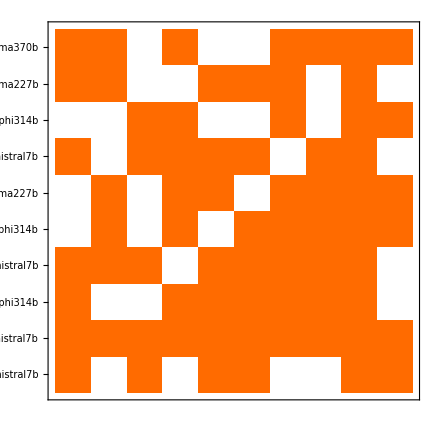

Wasserstein distance------------------------------------------------------------------------------------------

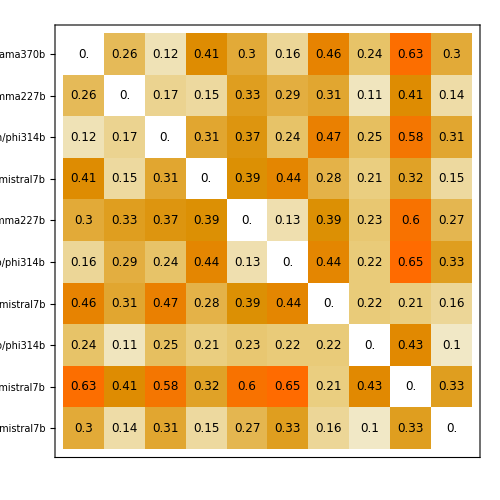

```mathematica
LocationEquivalenceTest[Values@finalMultisetDice,"TestDataTable"]

"dunn post-test--------------------------------------------------------------------------------"
dunnData = Dataset@DunnPostTest[finalMultisetDice];

finalMultisetDiceSignificant = Table[
Which[
m==n,
1,
m!=n,
If[First@Normal@dunnData[Select[(#["Group1"]==m && #["Group2"]==n)||(#["Group1"]==n && #["Group2"]==m)&]][;;,"p"]>.05,0,1]
],
{n,Keys@finalMultisetDice},{m,Keys@finalMultisetDice}
];


MatrixPlot[
finalMultisetDiceSignificant,
FrameTicks->{{Thread[{Range@Length@finalMultisetDiceSignificant,#[[1]]<>"/"<>#[[2]]&/@Keys@finalMultisetDice}],None},{None,Thread[{Range@Length@finalMultisetDiceSignificant,Rotate[#[[1]]<>"/"<>#[[2]],90Degree]&/@Keys@finalMultisetDice}]}},
FrameTicksStyle->14,
RotateLabel->True
]

"Wasserstein distance------------------------------------------------------------------------------------------"
finalMultisetDiceWassersteinDistance1D =Table[
WassersteinDistance1D[finalMultisetDice[m],finalMultisetDice[n]]["norm rescaled"],
{n,Keys@finalMultisetDice},{m,Keys@finalMultisetDice}
];

LabeledMatrixPlot[finalMultisetDiceWassersteinDistance1D,#[[1]]<>"/"<>#[[2]]&/@Keys@finalMultisetDice,90Degree]
```

Krippendorff's multiset Dice-Søresnen

{,,,,,,,,,}

{{{human,human}→1.,{human,llama370b}→0.284303,{human,gemma227b}→0.0409544,{human,phi314b}→0.255984,{human,mistral7b}→0.137273},{{llama370b,human}→0.284303,{llama370b,llama370b}→1.,{llama370b,gemma227b}→0.0832488,{llama370b,phi314b}→0.300715,{llama370b,mistral7b}→0.09666},{{gemma227b,human}→0.0409544,{gemma227b,llama370b}→0.0832488,{gemma227b,gemma227b}→1.,{gemma227b,phi314b}→0.0973348,{gemma227b,mistral7b}→-0.0446452},{{phi314b,human}→0.255984,{phi314b,llama370b}→0.300715,{phi314b,gemma227b}→0.0973348,{phi314b,phi314b}→1.,{phi314b,mistral7b}→0.236633},{{mistral7b,human}→0.137273,{mistral7b,llama370b}→0.09666,{mistral7b,gemma227b}→-0.0446452,{mistral7b,phi314b}→0.236633,{mistral7b,mistral7b}→1.}}

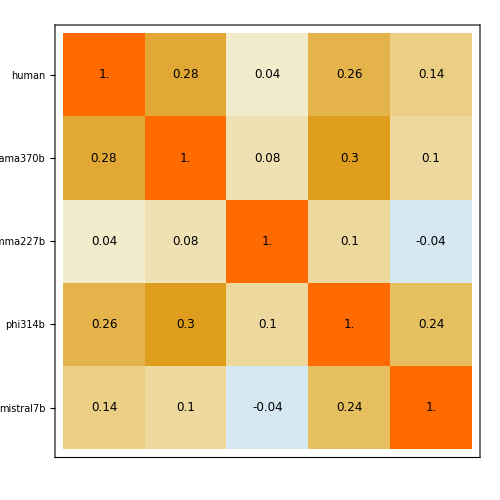

{,,,,,,,,,}

```mathematica
"Krippendorff's multiset Dice-Søresnen"
N@KrippendorffsAlpha[Values@finalResults,MultisetDiceSørensenDistance]

multisetDiceSørensenComparison = Table[
Prepend[N@KrippendorffsAlpha[{finalResults[s[[1]]],finalResults[s[[2]]]},MultisetDiceSørensenDistance],"coder"->s[[1]]<>"/"<>s[[2]]],
{s,Subsets[Keys@finalResults,{2}]}
]

krippendorffsMultiset =Table[
Table[
{i,j}->N@KrippendorffsAlpha[{finalResults[i],finalResults[j]},MultisetDiceSørensenDistance]["alpha"],
{j,Keys@finalResults}],
{i,Keys@finalResults}
]

LabeledMatrixPlot[Values@%,Keys@finalResults]
multisetDiceSørensenComparison
```